```mathematica
SetDirectory[NotebookDirectory[]];
all=FileNames[];
```

```mathematica
all//TableForm
```

new_test_slope.nb
NUMKINfitting_20-25_207.txt
NUMKINfitting_21-25_1836.txt
VARkinPmat-fitar2_1836.txt
VARkinPmat_fitar2_207.txt

```mathematica
Do[
data[i]=ToExpression[Import[all[[i]],"Lines"]];
,{i,2,Length[all]}]
```

```mathematica
(* electron in mp=207 *)
data2=Table[{data[2][[i,1]],SetPrecision[data[2][[i,2]],10]},{i,1,Length[data[2]]}];
fit2=NonlinearModelFit[data2,-a*x^2-c,{a,c},x,Method->"NMinimize"]
```

FittedModel[-0.4378169204-0.0002290889904 x^2]

```mathematica
fit22=FindFit[data2,-a*x^2-c,{a,c},x]
```

{a→0.0002435894113,c→0.4310129355}

```mathematica
nn2=TableForm[{{"m_p:","207"},{"ω:","0.02"},{"Particle:","Electron"},{"Fit Function:","-ar^2-b"},{"R^2:","0.999995"}}]
```

m_p: | 207
ω: | 0.02
Particle: | Electron
Fit Function: | -ar^2-b
R^2: | 0.999995

```mathematica
table2=Style[Grid[{{"","Estimate","Standard Error","Expectation","P-Value"},{a,0.000229,2.4744×10^-6,0.0002,1.1092×10^-56},{b,0.4378,0.0012,"-",1.2620×10^-84}},Alignment->{Left,Automatic},Dividers->{{2->GrayLevel[0.7]},{2->GrayLevel[0.7]}},ItemSize->{Automatic,Automatic},Spacings->{{2->1},{2->0.75}}],"DialogStyle"]
```

| Estimate | Standard Error | Expectation | P-Value
a | 0.000229 | 2.4744×10^-6 | 0.0002 | 1.1092×10^-56
b | 0.4378 | 0.0012 | - | 1.262×10^-84

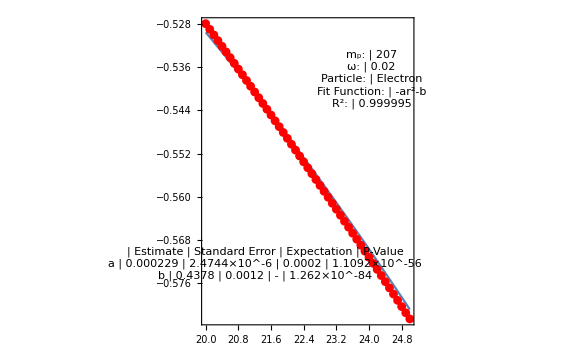

```mathematica
plot2=Show[Plot[fit2[x],{x,20,25},PlotRange->All],ListPlot[data2,PlotStyle->Red],ImageSize->Large,Frame->True,Epilog->{Inset[Framed[nn2],Scaled[{0.8,0.8}]],Inset[table2,Scaled[{0.3,0.2}]]}]
```

```mathematica
fit2["AdjustedRSquared"]
```

0.99999555

```mathematica
fit2["RSquared"]
```

0.999995724

```mathematica
fit2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0002290889904 | 2.47443×10^-6 | 92.5827 | 1.10921×10^-56
c | 0.4378169204 | 0.00126868 | 345.096 | 1.26202×10^-84

```mathematica
(* electron in mp=1836 *)
data3=Table[{data[3][[i,1]],SetPrecision[data[3][[i,2]],10]},{i,1,Length[data[3]]}];
fit3=NonlinearModelFit[data3,-a*x^2-c,{a,c},x,Method->"NMinimize"]
```

FittedModel[-0.4333367075-0.00009295244719 x^2]

```mathematica
fit33=FindFit[data3,-a*x^2-c,{a,c},x]
```

{a→0.00009229889826,c→0.433721478}

```mathematica
nn3=TableForm[{{"m_p:","1836"},{"ω:","0.01"},{"Particle:","Electron"},{"Fit Function:","-ar^2-b"},{"R^2:","0.999999"}}]
```

m_p: | 1836
ω: | 0.01
Particle: | Electron
Fit Function: | -ar^2-b
R^2: | 0.999999

```mathematica
table3=Style[Grid[{{"","Estimate","Standard Error","Expectation","P-Value"},{a,0.000092,4.2891×10^-7,0.00005,9.887603284353100075993`5.9789110082002255*^-75},{b,0.433336,0.0002,"-",7.272116359147649075492683522943657`5.978464057566352*^-121}},Alignment->{Left,Automatic},Dividers->{{2->GrayLevel[0.7]},{2->GrayLevel[0.7]}},ItemSize->{Automatic,Automatic},Spacings->{{2->1},{2->0.75}}],"DialogStyle"]
```

| Estimate | Standard Error | Expectation | P-Value
a | 0.000092 | 4.2891×10^-7 | 0.00005 | 9.8876×10^-75
b | 0.433336 | 0.0002 | - | 7.2721×10^-121

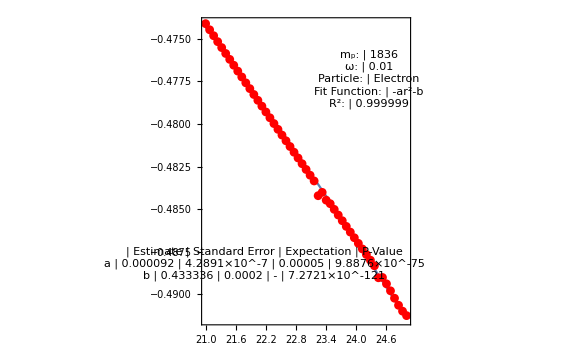

```mathematica
plot3=Show[Plot[fit3[x],{x,21,25},PlotRange->All],ListPlot[data3,PlotStyle->Red],ImageSize->Large,Frame->True,Epilog->{Inset[Framed[nn3],Scaled[{0.8,0.8}]],Inset[table3,Scaled[{0.3,0.2}]]}]
```

```mathematica
fit3["AdjustedRSquared"]
```

0.999999882

```mathematica
fit3["RSquared"]
```

0.999999886

```mathematica
fit3["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.00009295244719 | 4.28918×10^-7 | 216.714 | 9.8876×10^-75
c | 0.4333367075 | 0.000228676 | 1894.98 | 7.2721×10^-121

```mathematica
1/2*(0.02)^2
```

0.0002

```mathematica
1/2*(0.01)^2
```

0.00005

```mathematica
1/2*207*(0.02)^2
```

0.0414

```mathematica
1/2*1836*(0.01)^2
```

0.0918

```mathematica
(* PC in mp=1836 *)
data4=Table[{data[4][[i,1]],SetPrecision[data[4][[i,2]],10]},{i,1,26}];
fit4=NonlinearModelFit[data4,-a*x^2-c,{a,c},x,Method->"NMinimize"]
```

FittedModel[0.0150069-0.091898 x^2]

```mathematica
fit44=FindFit[data4,-a*x^2-c,{a,c},x]
```

{a→0.091898,c→-0.0150077}

```mathematica
nn4=TableForm[{{"m_p:","1836"},{"ω:","0.01"},{"Particle:","PC"},{"Fit Function:","-ar^2-b"},{"R^2:","1"}}]
```

m_p: | 1836
ω: | 0.01
Particle: | PC
Fit Function: | -ar^2-b
R^2: | 1

```mathematica
table4=Style[Grid[{{"","Estimate","Standard Error","Expectation","P-Value"},{a,0.091897,3.2266*^-9,0.0918,7.2514*^-164},{b,-0.015006,1.7123*^-7,0.015,1.3961*^-103}},Alignment->{Left,Automatic},Dividers->{{2->GrayLevel[0.7]},{2->GrayLevel[0.7]}},ItemSize->{Automatic,Automatic},Spacings->{{2->1},{2->0.75}}],"DialogStyle"]
```

| Estimate | Standard Error | Expectation | P-Value
a | 0.091897 | 3.2266×10^-9 | 0.0918 | 7.2514×10^-164
b | -0.015006 | 1.7123×10^-7 | 0.015 | 1.3961×10^-103

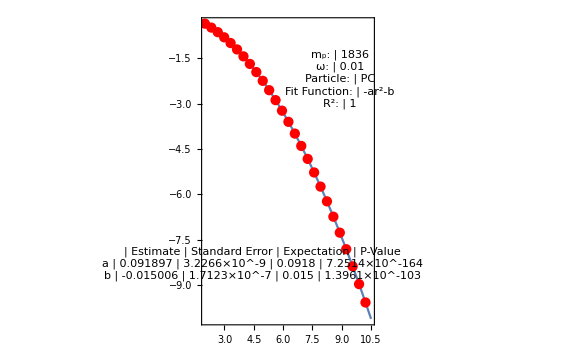

```mathematica
plot4=Show[Plot[fit4[x],{x,2,10.5},PlotRange->All],ListPlot[data4,PlotStyle->Red],ImageSize->Large,Frame->True,Epilog->{Inset[Framed[nn4],Scaled[{0.8,0.8}]],Inset[table4,Scaled[{0.35,0.2}]]}]
```

```mathematica
fit4["AdjustedRSquared"]
```

1.

```mathematica
fit4["RSquared"]
```

1.

```mathematica
fit4["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.091898 | 3.22661×10^-9 | 2.84813×10^7 | 7.25149×10^-164
c | -0.0150069 | 1.71233×10^-7 | -87640.5 | 1.39614×10^-103

```mathematica
Style[Grid[{{"","Estimate","Standard Error","t-Statistic","P-Value"},{a,0.091897,3.2266×10^-9,2.8481×10^7,7.251487036879978*^-164},{c,-0.015006903101171412,1.712325050462011*^-7,-87640.50433720119,1.396142979190212*^-103}},Alignment->{Left,Automatic},Dividers->{{2->GrayLevel[0.7]},{2->GrayLevel[0.7]}},ItemSize->{Automatic,Automatic},Spacings->{{2->1},{2->0.75}}],"DialogStyle"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.091897 | 3.2266×10^-9 | 2.8481×10^7 | 7.25149×10^-164
c | -0.0150069 | 1.71233×10^-7 | -87640.5 | 1.39614×10^-103

```mathematica
(* PC in mp=207 *)
data5=Table[{data[5][[i,1]],SetPrecision[data[5][[i,2]],10]},{i,1,26}];
fit5=NonlinearModelFit[data5,-a*x^2-c,{a,c},x,Method->"NMinimize"]
```

FittedModel[0.0301276-0.0417841 x^2]

```mathematica
fit55=FindFit[data5,-a*x^2-c,{a,c},x]
```

{a→0.0417841,c→-0.0301286}

```mathematica
nn5=TableForm[{{"m_p:","207"},{"ω:","0.02"},{"Particle:","PC"},{"Fit Function:","-ar^2-b"},{"R^2:","0.999999"}}]
```

m_p: | 207
ω: | 0.02
Particle: | PC
Fit Function: | -ar^2-b
R^2: | 0.999999

```mathematica
table5=Style[Grid[{{"","Estimate","Standard Error","Expectation","P-Value"},{a,0.041784,3.7553×10^-8,0.0414,4.5427×10^-130},{b,-0.030127,1.9929×10^-6,0.03,2.9012×10^-85}},Alignment->{Left,Automatic},Dividers->{{2->GrayLevel[0.7]},{2->GrayLevel[0.7]}},ItemSize->{Automatic,Automatic},Spacings->{{2->1},{2->0.75}}],"DialogStyle"]
```

| Estimate | Standard Error | Expectation | P-Value
a | 0.041784 | 3.7553×10^-8 | 0.0414 | 4.5427×10^-130
b | -0.030127 | 1.9929×10^-6 | 0.03 | 2.9012×10^-85

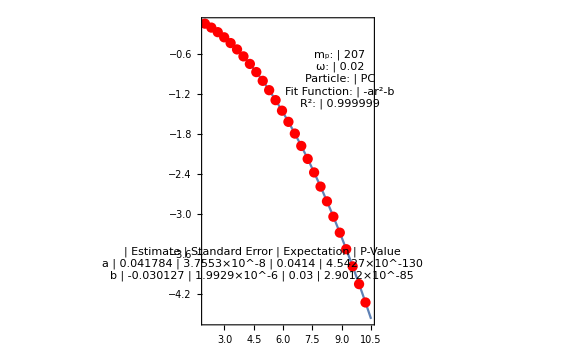

```mathematica
plot5=Show[Plot[fit5[x],{x,2,10.5},PlotRange->All],ListPlot[data5,PlotStyle->Red],ImageSize->Large,Frame->True,Epilog->{Inset[Framed[nn5],Scaled[{0.8,0.8}]],Inset[table5,Scaled[{0.35,0.2}]]}]
```

```mathematica
fit5["AdjustedRSquared"]
```

1.

```mathematica
fit5["RSquared"]
```

1.

```mathematica
fit5["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.0417841 | 3.7554×10^-8 | 1.11264×10^6 | 4.54275×10^-130
c | -0.0301276 | 1.99294×10^-6 | -15117.1 | 2.90123×10^-85

```mathematica
3/2*0.02
```

0.03

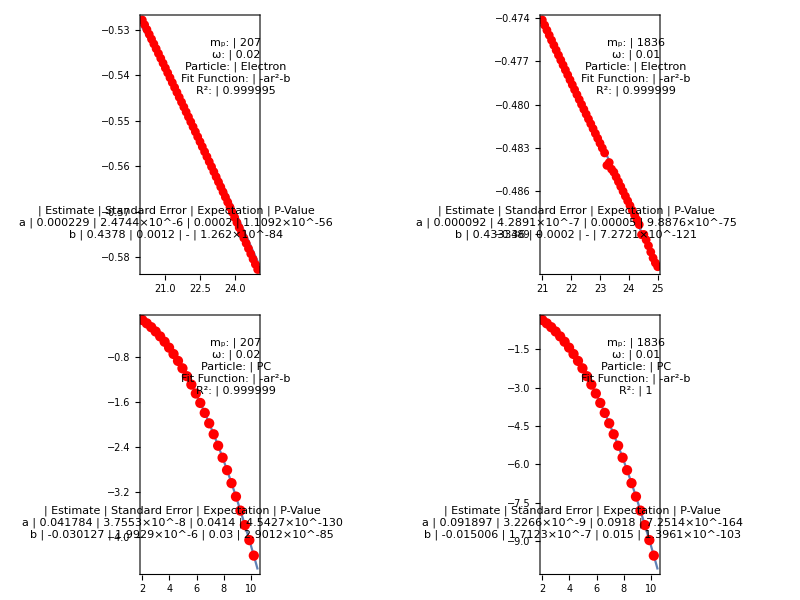

```mathematica
grid=Grid[{{plot2,plot3},{plot5,plot4}}]
```

```mathematica
Export["grid_ar3.png",grid]
```

grid_ar3.png